# Лабораторная 1. Знакомство с `Математикой’

Сохраните настоящий файл на СВОЕЙ флешке или в СВОЕМ Home, под своей фамилией с номером 1. Например, Ivanov1.nb. Выполняйте задания в сохраненном файле.

Задание 1. Напишите простейшую программу. Например, 3+7. Выполните ее. Закройте и откройте Выходную ячейку с помощью двойного щелчка левой кнопкой мыши.  Закройте и откройте Входную ячейку с помощью команды меню Cell/Cell Properties/Open. Как при этом меняется вид окаймляющей скобки?

```mathematica
3 + 7
```

10

Задание 2. С помощью окна Paletts/Other/Basic Math Input сформируйте команды
2^3
3/6
27^(1/3)
a=π
и выполните их. Очистите память командой меню Evaluation/Quit Kernel/Local, посмотрите текущее значение переменной a.

```mathematica
2^3
```

```mathematica
8
3/6
27^(1/3)
a=π
Clear[a]
a
```

8

1/2

3

π

a

Задание 3. Вычислите  значения констант E и Pi c 24 значащими цифрами с помощью команды N. Представьте в виде десятичных дробей числа Pi^(-20) и Pi^(-21). Что произойдет, если к этим числам применить команду Chop?

```mathematica
N[E, 24]
N[Pi, 24]
N[Pi^(-20)]
N[Pi^(-21)]
Chop[N[Pi^(-20)]]
Chop[N[Pi^(-21)]] // Очень маленькое число (из-за накопленных ошибок округления) приводится к 0
```

2.71828182845904523536029

3.14159265358979323846264

1.14026×10^-10

3.62955×10^-11

1.14026×10^-10

0

```mathematica
N[E,24]
N[Pi,24]
N[Pi^(-20)]
Chop[%]
N[Pi^(-21)]
Chop[%]
```

Задание 4. С помощью команды D (см. Help) найдите частную производную выражения x^5/y^7 по переменной y.

```mathematica
D[x^5/y^7, y]
Clear[x, y]
```

-(7 x^5)/y^8

```mathematica
D[x^5/y^7,y]
```

Задание 5. С помощью команды Integrate (см. Help) найдите определенный интеграл от функции x^5*Exp[x] по промежутку [0, 2]. Доведите вычисления до числа.

```mathematica
Integrate[x^5*Exp[x],{x,0,2}]
N[%]
```

Задание 6. С помощью команды Plot (см. Help) постройте график функции y = x^5*Exp[x] на промежутке [-12, 1].

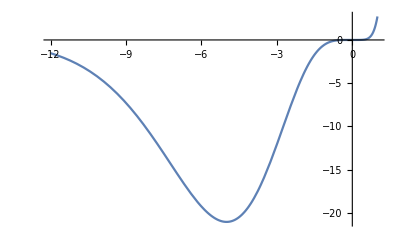

```mathematica
Plot[x^5*Exp[x], {x, -12, 1}]
Clear[x]
```

```mathematica
Plot[x^5*Exp[x],{x,-12,1},PlotRange->All]
```

Задание 7. С помощью команды Solve (см. Help) решите уравнение x^7 + x^3 - 3 = 0 ``в радикалах’’ и приближенно. Используйте команды Equal, N и ReplaceAll. С помощью команды Plot нарисуйте график функции y = x^7 + x^3 - 3 и проверьте предыдущий ответ. Как проверить комплексные корни? 
Замечание. Результатом работы команды Solve является подстановка (x -> 3), а не присвоение (x = 3). Это связано с тем, что повторный прогон программы без перезагрузки будет невозможен.

{{x→Root1.08Root[-3+#1^3+#1^7&,1]1.081804059559822},{x→Root-1.03-0.596 ⅈRoot[-3+#1^3+#1^7&,2]-1.0345429408971205},{x→Root-1.03+0.596 ⅈRoot[-3+#1^3+#1^7&,3]-1.0345429408971205},{x→Root-0.315-1.07 ⅈRoot[-3+#1^3+#1^7&,4]-0.3152979102637376},{x→Root-0.315+1.07 ⅈRoot[-3+#1^3+#1^7&,5]-0.3152979102637376},{x→Root0.809-0.954 ⅈRoot[-3+#1^3+#1^7&,6]0.8089388213809472},{x→Root0.809+0.954 ⅈRoot[-3+#1^3+#1^7&,7]0.8089388213809472}}

{x→Root1.08Root[-3+#1^3+#1^7&,1]1.081804059559822}

Root1.08Root[-3+#1^3+#1^7&,1]1.081804059559822

1.0818

{{x→1.0818},{x→-1.03454-0.595583 ⅈ},{x→-1.03454+0.595583 ⅈ},{x→-0.315298-1.06997 ⅈ},{x→-0.315298+1.06997 ⅈ},{x→0.808939-0.953764 ⅈ},{x→0.808939+0.953764 ⅈ}}

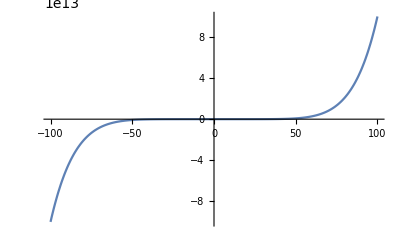

{}

```mathematica
solve = Solve[x^7 + x^3 - 3 == 0, x] (* Решение уравнения в радикалах *)
firstSolution = solve[[1]] (* Первая подстановка *)
firstValue = x /. solve[[1]] (* Первое значение *)
N[firstValue]

numericalSolve = N[solve] (* Приближенное численное решение *)
Plot[x^7 + x^3 - 3 == 0, {x, -100, 100}, PlotRange->All]
complexSolve = Select[solve, !FreeQ[x /. #, Complex]&] (* # - анонимная переменная списка solve, & - конце анонимной функции*)
```

```mathematica
sol=Solve[x^7+x^3-3==0,x]
x/.sol
roots=N[%]
points=Transpose[{Re[#],Im[#]}]&[roots];
ListPlot[points]
Plot[x^7+x^3-3,{x,-5,5}]
Plot[x^7+x^3-3//ArcTan,{x,-5,5}]
x^7+x^3-3/.sol//N
```

Задание 8. Прочитайте в Help, чем отличаются команды Solve, Root, FindRoot, NSolve? Как решить систему уравнений? Что делают команды Eliminate и Reduce?

```mathematica
Solve[x^2 - 4 == 0, x]
NSolve[x^2 - 4 == 0, x]
FindRoot[x^2-4==0,{x,1}]
Solve[x^5-2==0,x]
Solve[x^5-2==0,x]
Root[-2+#1^5&,1]
Eliminate[{x+y==5,x-y==1},x]
Reduce[x^2-4==0,x]
```

{{x→-2},{x→2}}

{{x→-2.},{x→2.}}

{x→2.}

{{x→-(-2)^(1/5)},{x→2^(1/5)},{x→(-1)^(2/5) 2^(1/5)},{x→-(-1)^(3/5) 2^(1/5)},{x→(-1)^(4/5) 2^(1/5)}}

{{x→-(-2)^(1/5)},{x→2^(1/5)},{x→(-1)^(2/5) 2^(1/5)},{x→-(-1)^(3/5) 2^(1/5)},{x→(-1)^(4/5) 2^(1/5)}}

Root1.15Root[-2+#1^5&,1]1.148698354997035

y==2

x==-2||x==2

1. Команда Solve используется для нахождения символического решения уравнений. Она возвращает корни уравнений в виде подстановок (правил вида x -> значение).
Solve[x^2 - 4 == 0, x]
Результат: {{x -> -2}, {x -> 2}}

2. Команда NSolve предназначена для нахождения численных решений уравнений или систем уравнений.
NSolve[x^2 - 4 == 0, x]
Результат: {{x→-2.},{x→2.}}

3. Команда FindRoot используется для нахождения численных решений уравнений, но с тем отличием, что она требует начального приближения.
Результат: {x→2.}

4. Root — возвращает компактное представление корней уравнений, если они не могут быть выражены через радикалы.

5. Команда Eliminate используется для исключения одной или нескольких переменных из системы уравнений. Она убирает указанные переменные и возвращает выражения, которые не содержат эти переменные.
Eliminate[{x + y == 5, x - y == 1}, x]
Результат: y == 2

6. Команда Reduce даёт более полное описание решения уравнений или системы уравнений. Она возвращает условия, при которых решения возможны, и может предоставлять решения в виде логических утверждений.
Reduce[x^2 - 4 == 0, x]
Результат: x == -2 || x == 2

Задание 9. Прочитайте в Help, какие опции имеет команда Solve. C помощью опции WorkingPrecision найдите значение корней уравнения x^7+x^3-3=0 со 100 значащими цифрами.

```mathematica
NSolve[x^7 + x^3 - 3 == 0, x, WorkingPrecision-> 100]
```

{{x→-1.034542940897120536874103227729376148929517005094053208471751829894565221644614358539451897408760588-0.59558284436971059885009379768300553351659551559258131865125456335334988386953756659702615472063607 ⅈ},{x→-1.034542940897120536874103227729376148929517005094053208471751829894565221644614358539451897408760588+0.59558284436971059885009379768300553351659551559258131865125456335334988386953756659702615472063607 ⅈ},{x→-0.315297910263737593456949733877393091241799479034905584667244770233433814328396318068895102782099157-1.069971785417535646123988640214113342368377530581741661510489566931516580064066424167514335485279061 ⅈ},{x→-0.315297910263737593456949733877393091241799479034905584667244770233433814328396318068895102782099157+1.069971785417535646123988640214113342368377530581741661510489566931516580064066424167514335485279061 ⅈ},{x→0.808938821380947208322384788427031330549708957334140134934569854238509395479028312708737873412792373-0.9537637815816295685246094404637411433449449014171199560747772505373540160003129008832942917459854565 ⅈ},{x→0.808938821380947208322384788427031330549708957334140134934569854238509395479028312708737873412792373+0.9537637815816295685246094404637411433449449014171199560747772505373540160003129008832942917459854565 ⅈ},{x→1.081804059559821844017336346359475819243215053589637316408853491778979280987964727799218253556134746}}

```mathematica
sol=Solve[x^7+x^3-3==0,x,WorkingPrecision->100]
```

Задание 10. С помощью команд Timing и AbsoluteTime установите, сколько времени уходит на нахождение корней уравнения x^7+x^3-3=0 со 100 значащими цифрами. Очистите память с помощью команды меню Evaluation/Quit Kernel/Local, а затем выполните свою программу дважды. Чем объяснить различное время счета?
   Указание. Внимательно прочитайте, что является аргументами команд Timing и AbsoluteTime.

```mathematica
(*Timing*)
timingResult=Timing[NSolve[x^7+x^3-3==0,x,WorkingPrecision->100]]

(*AbsoluteTime*)
startTime=AbsoluteTime[];
numericalSolution=NSolve[x^7+x^3-3==0,x,WorkingPrecision->100];
endTime=AbsoluteTime[];

(*Вычисление реального времени выполнения*)
absoluteTimeElapsed=endTime-startTime;

Print["Timing: ",timingResult[[1]]," секунд"];
Print["AbsoluteTime: ",absoluteTimeElapsed," секунд"];
```

{0.,{{x→-1.034542940897120536874103227729376148929517005094053208471751829894565221644614358539451897408760588-0.59558284436971059885009379768300553351659551559258131865125456335334988386953756659702615472063607 ⅈ},{x→-1.034542940897120536874103227729376148929517005094053208471751829894565221644614358539451897408760588+0.59558284436971059885009379768300553351659551559258131865125456335334988386953756659702615472063607 ⅈ},{x→-0.315297910263737593456949733877393091241799479034905584667244770233433814328396318068895102782099157-1.069971785417535646123988640214113342368377530581741661510489566931516580064066424167514335485279061 ⅈ},{x→-0.315297910263737593456949733877393091241799479034905584667244770233433814328396318068895102782099157+1.069971785417535646123988640214113342368377530581741661510489566931516580064066424167514335485279061 ⅈ},{x→0.808938821380947208322384788427031330549708957334140134934569854238509395479028312708737873412792373-0.9537637815816295685246094404637411433449449014171199560747772505373540160003129008832942917459854565 ⅈ},{x→0.808938821380947208322384788427031330549708957334140134934569854238509395479028312708737873412792373+0.9537637815816295685246094404637411433449449014171199560747772505373540160003129008832942917459854565 ⅈ},{x→1.081804059559821844017336346359475819243215053589637316408853491778979280987964727799218253556134746}}}

Timing: 0. секунд

AbsoluteTime: 0.0009993 секунд

```mathematica
Timing[N[Solve[x^7+x^3-3==0,x,WorkingPrecision->100],100]] 
t0=AbsoluteTime[];
N[Solve[x^7+x^3-3==0,x,WorkingPrecision->100],100]
AbsoluteTime[]-t0
```

Задание 11. Предложите пример, иллюстрирующий отличие команд Precision и Accuracy.
1. Precision измеряет общее количество значащих цифр в числе, то есть количество всех цифр, включая и целую, и дробную части.
2. Accuracy измеряет точность числовых значений относительно десятичной точки — сколько знаков после запятой передаются точно.

```mathematica
num3=SetPrecision[123.456,10];
num4=SetAccuracy[123.456,10];
num3
num4
Precision[num3]
Accuracy[num4]
```

123.456

123.456

10.

10.

```mathematica
a=N[10^10*Pi,20]
Precision[a]
Accuracy[a]
```

Задание 12. Присвойте последовательным переменным x1, x2, ..., x7 значения корней уравнения x^7 + x^3 - 3 = 0 (можно использовать команду Do).

```mathematica
Print[Style["Решение 1",24,Blue]];
sol=Solve[z^7+z^3-3==0,z]
z/.sol
roots=N[%]
{x1,x2,x3,x4,x5,x6,x7}=roots
Print["Проверка: x3=",x3];

Print[Style["Решение 2",24,Blue]];
Do[x[i]=roots[[i]],{i,Length[roots]}];
Print["Проверка: x3=",x3];

Print[Style["Решение 3",24,Blue]];
Do[Print[Subscript[x,i]," = ",roots[[i]]],{i,Length[roots]}];
```

```mathematica
solve = NSolve[x^7 + x^3 - 3 == 0, x]
Do[
Subscript[x, i] = solve[[i]], {i, 1, 7}
]
```

{{x→-1.03454-0.595583 ⅈ},{x→-1.03454+0.595583 ⅈ},{x→-0.315298-1.06997 ⅈ},{x→-0.315298+1.06997 ⅈ},{x→0.808939-0.953764 ⅈ},{x→0.808939+0.953764 ⅈ},{x→1.0818}}

Do::nliter: Non-list iterator {i,1,7} x_i at position 2 does not evaluate to a real numeric value.

Do[x_i=solve⟦i⟧,{i,1,7} x_i]

```mathematica
solve = NSolve[x^7 + x^3 - 3 == 0, x]

vars = Association[];

Do[
vars[Symbol["x" <> ToString[i]]] = x /. solve[[i]],
{i, 1, Length[solve]}
]

vars
```

{{x→-1.03454-0.595583 ⅈ},{x→-1.03454+0.595583 ⅈ},{x→-0.315298-1.06997 ⅈ},{x→-0.315298+1.06997 ⅈ},{x→0.808939-0.953764 ⅈ},{x→0.808939+0.953764 ⅈ},{x→1.0818}}

<|x1→-1.03454-0.595583 ⅈ,x2→-1.03454+0.595583 ⅈ,x3→-0.315298-1.06997 ⅈ,x4→-0.315298+1.06997 ⅈ,x5→0.808939-0.953764 ⅈ,x6→0.808939+0.953764 ⅈ,x7→1.0818|>

x1